## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = True;

rxnName="PFK1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PFK1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 1 | 0.95
1.05 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 110.7 | 108.1
113.3 | 1/s | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 | 
1 | Kic | adp | 0.0002 | 0.00019
0.00021 |  | Competitive | atp | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | adp | 0.000025 | 0.00002375
0.00002625 |  |  | M | 8.5 | 28 | tris | 0.05 | 
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n |  | 2.11 | 2.
2.22 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  | 8.5 | 28 | tris | 0.05 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.1};
s05Priorities = {0.8};
kcatPriorities = {0.2};
inhibitionPriorities={0.1,0.2};
activationPriorities = {0.5,0.6};
otherParamsPriorities = {0.14,0.5};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 1 | 0.95
1.05 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
0.1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.8 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.2 | gdp | 0.001
atp | Null
f6p | Null | 110.7 | 108.1
113.3 | 1/s | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 | 
0.2 | Kic | adp | 0.0002 | 0.00019
0.00021 |  | Competitive | atp | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.5 | Ka | adp | 0.000025 | 0.00002375
0.00002625 |  |  | M | 8.5 | 28 | tris | 0.05 | 
0.6 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.14 | n |  | 2.11 | 2.
2.22 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
0.5 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  | 8.5 | 28 | tris | 0.05 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
(*catalyticBranch={"E_PFK1[c] + atp[c] <=> E_PFK1[c]&atp",
				"E_PFK1[c]&atp + f6p[c] <=> E_PFK1[c]&atp&f6p",
				
				"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&atp&f6p",

				"E_PFK1[c]&atp&f6p <=> E_PFK1[c]&fdp&adp",
				
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};*)

catalyticBranch={"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&atp&f6p",

				"E_PFK1[c]&atp&f6p <=> E_PFK1[c]&fdp&adp",
				
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["gdp", "c"], m["adp","c"]},ActivationSites->1,Inhibitors->{m["pep", "c"]},InhibitionSites->1];
enzymeModel["Reactions"]
```

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&atp^c&f6p^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&atp^c&f6p^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(adp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(adp^c))^PFK11$22,((PFK1^c&fdp^c)_^(adp^c)⇌(PFK1^c)_^(adp^c)+fdp^c)^PFK12$22,((PFK1^c&f6p^c)_^(adp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(adp^c))^PFK13$22,((PFK1^c&fdp^c&adp^c)_^(adp^c)⇌(PFK1^c&fdp^c)_^(adp^c)+adp^c)^PFK14$22,((PFK1^c&atp^c&f6p^c)_^(adp^c)⇌(PFK1^c&fdp^c&adp^c)_^(adp^c))^PFK15$22,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$24,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$24,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^c))^PFK13$24,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$24,((PFK1^c&atp^c&f6p^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$24,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$25,((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$26,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$27,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,Overscript[(PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c, PFK12],((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&atp^c&f6p^c)_^)^PFK13,Overscript[(PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c, PFK14],((PFK1^c&atp^c&f6p^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15};
catalyticReactionsSet2 ={Overscript[(PFK1^c)_^(adp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(adp^c), PFK11$14],Overscript[(PFK1^c&fdp^c)_^(adp^c)⇌(PFK1^c)_^(adp^c)+fdp^c, PFK12$14],Overscript[(PFK1^c&f6p^c)_^(adp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(adp^c), PFK13$14],Overscript[(PFK1^c&fdp^c&adp^c)_^(adp^c)⇌(PFK1^c&fdp^c)_^(adp^c)+adp^c, PFK14$14],Overscript[(PFK1^c&atp^c&f6p^c)_^(adp^c)⇌(PFK1^c&fdp^c&adp^c)_^(adp^c), PFK15$14]};

catalyticReactionsSet3 ={ Overscript[(PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c), PFK11$15],Overscript[(PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c, PFK12$15],Overscript[(PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^c), PFK13$15],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c, PFK14$15],Overscript[(PFK1^c&atp^c&f6p^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c), PFK15$15]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
MWCFlag=True;
nActiveSites=1;
simplifyMaxTime=7200;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_adp",fdp^c->0}};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,{inhibitionList[[2]]}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

Power::infy: Infinite expression 1/0 encountered.

```mathematica
nonCatalyticReactions
```

{((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$8,((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$11,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

```mathematica
MWCFlag=True;
nActiveSites=1;
simplifyMaxTime=7200;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_adp",fdp^c->0}};
otherMetsForwardZeroSub={};
```

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
	If[ !SameQ[inhibitionList, {}],
		inhibitors = inhibitionList[[All,2]];
		prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];,
		prodInhibBool = False;
	];

	{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
	rates = getEnzymeRates[enzymeModel];
	{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

	{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModel];
	
	unifiedRateConstList = 
		If[TrueQ[MWCFlag],
			getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions],
			{}
		];
			
	(*Identify Transition Rate Equations*)
	transitionID = getTransitionIDs[allCatalyticReactions];

	(*Extract Transition Rate Equations*)
	transitionRateEqs = getTransitionRateEqs[transitionID, rates];
```

```mathematica
unifiedRateConstList
```

{k_PFK11^⟶→k_PFK11^⟶,k_PFK11^⟵→k_PFK11^⟵,k_PFK12^⟶→k_PFK12^⟶,k_PFK12^⟵→k_PFK12^⟵,k_PFK13^⟶→k_PFK13^⟶,k_PFK13^⟵→k_PFK13^⟵,k_PFK14^⟶→k_PFK14^⟶,k_PFK14^⟵→k_PFK14^⟵,k_PFK15^⟶→k_PFK15^⟶,k_PFK15^⟵→k_PFK15^⟵,k_PFK16^⟶→k_PFK16^⟶,k_PFK16^⟵→k_PFK16^⟵,k_PFK17^⟶→k_PFK17^⟶,k_PFK17^⟵→k_PFK17^⟵,k_PFK11$3^⟶→k_PFK11^⟶,k_PFK11$3^⟵→k_PFK11^⟵,k_PFK12$3^⟶→k_PFK12^⟶,k_PFK12$3^⟵→k_PFK12^⟵,k_PFK13$3^⟶→k_PFK13^⟶,k_PFK13$3^⟵→k_PFK13^⟵,k_PFK14$3^⟶→k_PFK14^⟶,k_PFK14$3^⟵→k_PFK14^⟵,k_PFK15$3^⟶→k_PFK15^⟶,k_PFK15$3^⟵→k_PFK15^⟵,k_PFK16$3^⟶→k_PFK16^⟶,k_PFK16$3^⟵→k_PFK16^⟵,k_PFK17$3^⟶→k_PFK17^⟶,k_PFK17$3^⟵→k_PFK17^⟵,k_PFK11$7^⟶→k_PFK11^⟶,k_PFK11$7^⟵→k_PFK11^⟵,k_PFK12$7^⟶→k_PFK12^⟶,k_PFK12$7^⟵→k_PFK12^⟵,k_PFK13$7^⟶→k_PFK13^⟶,k_PFK13$7^⟵→k_PFK13^⟵,k_PFK14$7^⟶→k_PFK14^⟶,k_PFK14$7^⟵→k_PFK14^⟵,k_PFK15$7^⟶→k_PFK15^⟶,k_PFK15$7^⟵→k_PFK15^⟵,k_PFK16$7^⟶→k_PFK16^⟶,k_PFK16$7^⟵→k_PFK16^⟵,k_PFK17$7^⟶→k_PFK17^⟶,k_PFK17$7^⟵→k_PFK17^⟵,k_PFK1_Activation_gdp$8^⟶→k_PFK1_Activation_gdp^⟶,k_PFK1_Activation_gdp$8^⟵→k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_adp$10^⟶→k_PFK1_Activation_adp^⟶,k_PFK1_Activation_adp$10^⟵→k_PFK1_Activation_adp^⟵,k_PFK1_Inhibition_pep$11^⟶→k_PFK1_Inhibition_pep^⟶,k_PFK1_Inhibition_pep$11^⟵→k_PFK1_Inhibition_pep^⟵,k_PFK1_TransitionStep^⟶→k_PFK1_TransitionStep^⟶,k_PFK1_TransitionStep^⟵→k_PFK1_TransitionStep^⟵}

```mathematica
simplifyMaxTime=70000;
	(*King-Altman Workaround UsingMathematicaSolve*)
	(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
	MemoryConstrained[absoluteFluxNoProdInhib=
		If[prodInhibBool,
			Print["prod inhib"];
			getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs,simplifyMaxTime,nActiveSites, "NoProdInhibRefactor"],
			Null
		];,12000000000];//AbsoluteTiming
```

prod inhib

```mathematica
{enzymeModel,nonCatalyticReactions} = addInhibitionReactions[enzymeModel,rxnName,{inhibitionList[[2]]},allCatalyticReactions,nonCatalyticReactions];

	Print["abs flux"];
	(* get flux equation including inhibitions*)
	absoluteFlux = getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];

	{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} = 
		getRateEqs[absoluteFlux, unifiedRateConstList, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub, 
					absoluteFluxNoProdInhib, absoluteFluxNoProdInhib,otherMetsForwardZeroSub, otherMetsReverseZeroSub];

	(* set up haldane relations *)
	haldaneRatiosList  = Table[
				haldane = haldaneRelation[KeqName,catalyticReactionsSet]/.unifiedRateConstList;
				haldane[[2]],
		{catalyticReactionsSet, catalyticReactionsSetsList}];


	(*Assemble Rate Constant And Metabolite Substitutions for Export*)
	{finalRateConsts,metsFull, metsSub, rateConstsSub} = 
			getMetRatesSubs[enzymeModel, haldaneRatiosList, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse,KeqVal,otherAbsoluteRatesForward, otherAbsoluteRatesReverse];

	(*Export Equations*)
	{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub} = 
			exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub,
							otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["PFK1SimulateDataArguments.mx",{enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["PFK1SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"]
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

```mathematica
FilePrint@dataPathList
```

### Simulate data with uncertainty

```mathematica
Export["PFK1SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

{0.073096}

{0.073096}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	3.2619726608494514e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	5.169878264174563e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.1368068886032102
0	8.193704866742945e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310203
0	0.000012986147064336368	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.28474724895080145
0	0.000020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.3868631798468571
0	0.00003261972660849452	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00005169878264174563	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531434
0	0.00008193704866742946	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491989
0	0.00012986147064336382	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.00020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.8631931113967901
0	0.00032619726608494517	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	5.059566229935254e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007970767124361075
0	0.001	8.018872074630528e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020649925137307165
0	0.001	0.000012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.05243192591019078
0	0.001	0.000020142495960275474	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12679610799805113
0	0.001	0.00003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27591931027727645
0	0.001	0.00005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.4999999999999996
0	0.001	0.00008018872074630527	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7240806897227228
0	0.001	0.00012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8732038920019485
0	0.001	0.00020142495960275497	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9475680740898091
0	0.001	0.0003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9793500748626928
0	0.001	0.0005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9920292328756389
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0.00010467341096543913	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.00010467341096543913	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.00010467341096543913	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.00010467341096543913	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.00010467341096543913	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.00020934682193087827	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.00020934682193087827	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.00020934682193087827	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.00020934682193087827	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.00020934682193087827	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.00041869364386175654	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.00041869364386175654	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.00041869364386175654	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.00041869364386175654	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.00041869364386175654	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6

### Parameter scan

```mathematica
Export["PFK1ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"s05",1,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"activation",1,{0.001,1,100}},
				{"other",1,{1,3,4}},
				{"other",2,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

{0.073096}

{0.073096}

«15 more identical outputs»

```mathematica
FilePrint@dataPathList[[16]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	9.000000000000007e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	0.000014264038732150038	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.13680688860321014
0	0.000022606977883586257	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310197
0	0.00003582964534981475	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.2847472489508014
0	0.00005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.38686317984685703
0	0.00009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00014264038732150037	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531432
0	0.00022606977883586258	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491988
0	0.00035829645349814786	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.0005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.86319311139679
0	0.0009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	9.000000000000007e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007702679340006974
0	0.001	0.000014264038732150038	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020099351492257313
0	0.001	0.000022606977883586257	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.051413474162681154
0	0.001	0.00003582964534981475	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12527679844770145
0	0.001	0.00005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27454359645655
0	0.001	0.00009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.5000000000000004
0	0.001	0.00014264038732150037	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7254564035434503
0	0.001	0.00022606977883586258	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8747232015522989
0	0.001	0.00035829645349814786	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9485865258373192
0	0.001	0.0005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9799006485077427
0	0.001	0.0009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.992297320659993
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0.0001	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.0001	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.0001	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.0001	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.0001	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.0002	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.0002	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.0002	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.0002	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.0002	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.0004	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.0004	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.0004	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.0004	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.0004	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] //AbsoluteTiming
```

{53.9959,best_fit: 8.01348237122}

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFileName, lmaResultsFileName, numTrials, dataPathList]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFileName;
dataFilePath = dataPath;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileName, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
relRateFor_fdp | 0.0338777 | 0.0011477 | 7.50414 | 0.0909091 | 0.0840871
relRateFor_fdp | 0.0322292 | 0.00103872 | 7.15237 | 0.136807 | 0.127022
relRateFor_fdp | 0.0299217 | 0.000895307 | 6.65774 | 0.20076 | 0.187394
relRateFor_fdp | 0.0268726 | 0.000722136 | 6.00009 | 0.284747 | 0.267662
relRateFor_fdp | 0.0231363 | 0.000535287 | 5.18791 | 0.386863 | 0.366793
relRateFor_fdp | 0.0189588 | 0.000359437 | 4.27152 | 0.5 | 0.478642
relRateFor_fdp | 0.0147408 | 0.000217292 | 3.33724 | 0.613137 | 0.592675
relRateFor_fdp | 0.0108982 | 0.000118771 | 2.47818 | 0.715253 | 0.697528
relRateFor_fdp | 0.00771207 | 0.000059476 | 1.7601 | 0.79924 | 0.785173
relRateFor_fdp | 0.00527018 | 0.0000277748 | 1.20617 | 0.863193 | 0.852782
relRateFor_fdp | 0.00350919 | 0.0000123144 | 0.804765 | 0.909091 | 0.901775
relRateFor_fdp | 0.0338777 | 0.0011477 | 7.50414 | 0.0909091 | 0.0840871
relRateFor_fdp | 0.0322292 | 0.00103872 | 7.15237 | 0.136807 | 0.127022
relRateFor_fdp | 0.0299217 | 0.000895307 | 6.65774 | 0.20076 | 0.187394
relRateFor_fdp | 0.0268726 | 0.000722136 | 6.00009 | 0.284747 | 0.267662
relRateFor_fdp | 0.0231363 | 0.000535287 | 5.18791 | 0.386863 | 0.366793
relRateFor_fdp | 0.0189588 | 0.000359437 | 4.27152 | 0.5 | 0.478642
relRateFor_fdp | 0.0147408 | 0.000217292 | 3.33724 | 0.613137 | 0.592675
relRateFor_fdp | 0.0108982 | 0.000118771 | 2.47818 | 0.715253 | 0.697528
relRateFor_fdp | 0.00771207 | 0.000059476 | 1.7601 | 0.79924 | 0.785173
relRateFor_fdp | 0.00527018 | 0.0000277748 | 1.20617 | 0.863193 | 0.852782
relRateFor_fdp | 0.00350919 | 0.0000123144 | 0.804765 | 0.909091 | 0.901775
relRateFor_fdp | 0.146487 | 0.0214584 | 40.1157 | 0.0909091 | 0.127378
relRateFor_fdp | 0.137779 | 0.018983 | 37.3342 | 0.136807 | 0.187883
relRateFor_fdp | 0.125929 | 0.0158581 | 33.6377 | 0.20076 | 0.268291
relRateFor_fdp | 0.110843 | 0.0122861 | 29.0752 | 0.284747 | 0.367538
relRateFor_fdp | 0.0931792 | 0.00868236 | 23.9308 | 0.386863 | 0.479443
relRateFor_fdp | 0.0744132 | 0.00553733 | 18.6898 | 0.5 | 0.593449
relRateFor_fdp | 0.0564247 | 0.00318374 | 13.874 | 0.613137 | 0.698204
relRateFor_fdp | 0.0408044 | 0.001665 | 9.85109 | 0.715253 | 0.785713
relRateFor_fdp | 0.0283653 | 0.00080459 | 6.74936 | 0.79924 | 0.853184
relRateFor_fdp | 0.0191267 | 0.000365832 | 4.50251 | 0.863193 | 0.902058
relRateFor_fdp | 0.0126155 | 0.000159151 | 2.94743 | 0.909091 | 0.935886
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936

### Simulated Data and Best Fit Data Plot

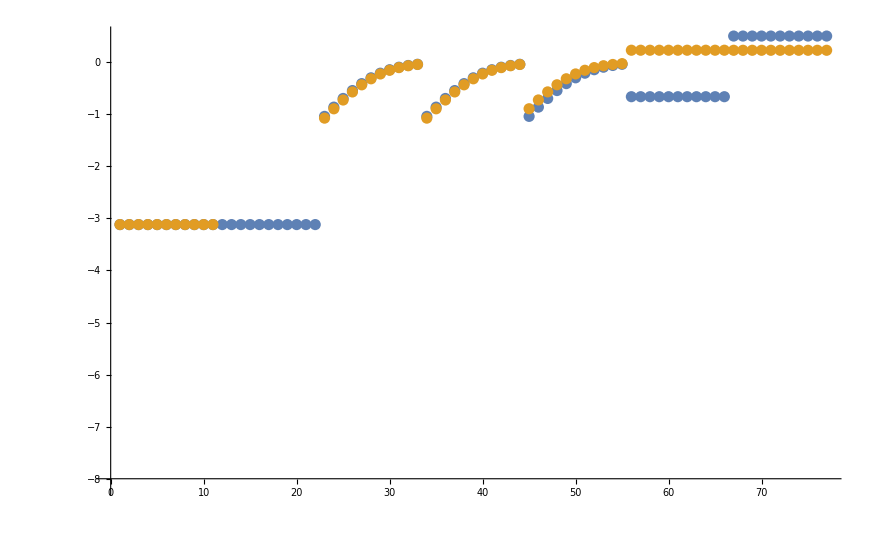

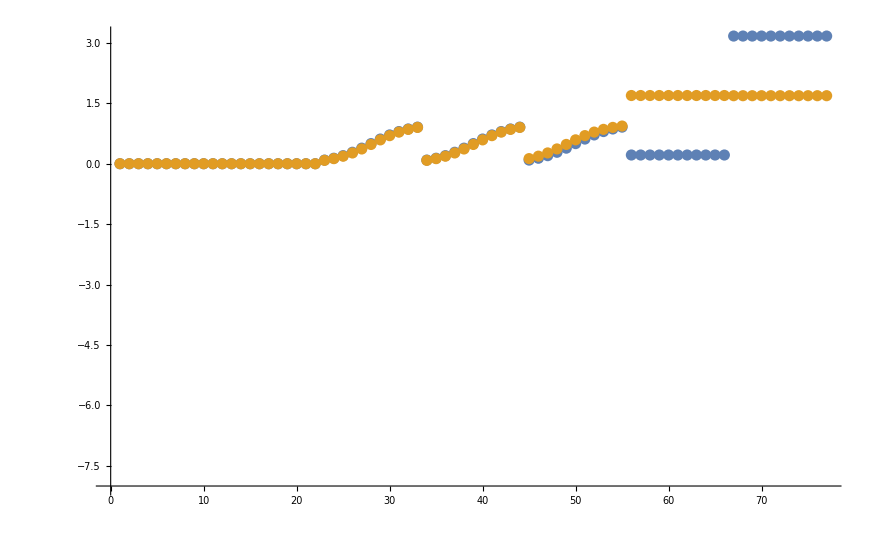

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

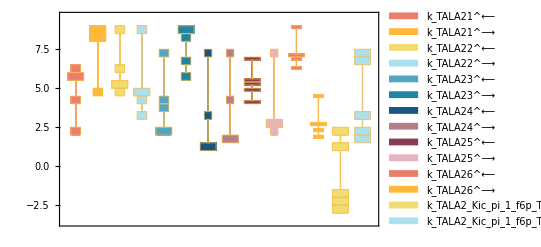

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

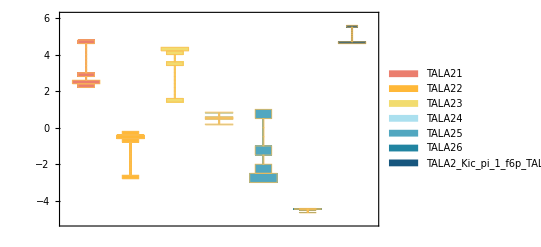

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

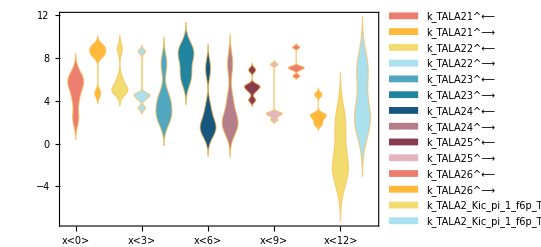

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

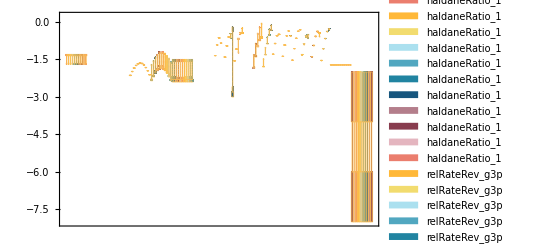

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138

```mathematica
backCalculateRatios[haldaneRatiosList[[2]][[1]], haldaneRatiosList[[2]][[2]], paramFitSub]//TableForm
```